```mathematica
Clear["Global`*"]
```

```mathematica
pt={{-1,-1/Sqrt[3]},{1,-1/Sqrt[3]},{0,2/3*Sqrt[3]}};
ptMid={(pt[[1]]+pt[[2]])/2,(pt[[2]]+pt[[3]])/2,(pt[[3]]+pt[[1]])/2};
```

```mathematica
t1=ArcTan[Sqrt[3]/2];
t2=ArcTan[Sqrt[3]*2];
pstart1=ptMid[[1]] + 0.8*{Cos[t1],Sin[t1]};
pstart2=ptMid[[1]] + 0.8*{Cos[t2],Sin[t2]};
```

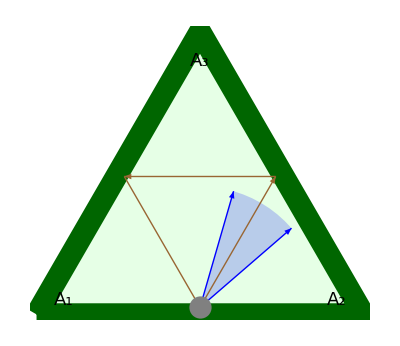

```mathematica
g1=Graphics[{Lighter[Green,0.9],EdgeForm[{Darker[Green,0.6],Thickness[0.04],JoinForm["Round"]}],Polygon[pt*1.08]}];
g2=Graphics[{Opacity[0.2],Blue,Disk[ptMid[[1]],0.8,{t1,t2}]}];
g3=Graphics[{Thick, Brown,Arrow[{ptMid[[1]],ptMid[[2]]}],Arrow[{ptMid[[2]],ptMid[[3]]}],Arrow[{ptMid[[3]],ptMid[[1]]}]}];
g4=Graphics[{Thick,Blue,Arrow[{ptMid[[1]],pstart1}],Arrow[{ptMid[[1]],pstart2}]}];
g5=Graphics[{Gray,PointSize[0.04],Point[ptMid[[1]]]}];
g6=Graphics[{Text[Style["A_1",18,FontFamily->"Times New Roman"],pt[[1]]+{0.1,0.05}],
Text[Style["A_2",18,FontFamily->"Times New Roman"],pt[[2]]+{-0.1,0.05}],
Text[Style["A_3",18,FontFamily->"Times New Roman"],pt[[3]]+{0,-0.1}]}];
Show[g1,g2,g3,g4,g5,g6,ImageSize->400]
```

```mathematica
t1/Pi*180//N[#,20]&
t2/Pi*180//N[#,20]&
```

40.893394649130905605

73.897886248013984716